# Homework 25

## Problem 25.1

A turntable spins with angular velocity Omega in the +z direction. A bee flies past at a position in the lab frame given by (a*t^2/2,y0,0) for t > 0. Find the position, velocity, and acceleration of the bee as a function of time, as measured by an observer on the turntable. 
(A) Do the problem using a rotation matrix and derivatives.
(B) Do the problem using the Eq. 9.34.
(C) Graph the bee's trajectory and velocity as observed in the turntable frame.


Let a = 0.50 m/s^2 and y0 = 1.0 cm.

Let Ovec be the angular velocity vector.

```mathematica
Clear["`*"]
```

We call the lab S0 and the turntable S. To convert from turntable to lab coordinates, we need to use the rotation matrix R. < lab vector >= R < turntable vector > or < turntable vector >= R inverse < lab vector > .

```mathematica
R={{Cos[Omega*t],-Sin[Omega*t],0},{Sin[Omega*t],Cos[Omega*t],0},{0,0,1}};
R//MatrixForm
RI=FullSimplify[Inverse[R]];
RI//MatrixForm
FullSimplify[R.RI]//MatrixForm
```

(Cos[Omega t] | -Sin[Omega t] | 0
Sin[Omega t] | Cos[Omega t] | 0
0 | 0 | 1)

(Cos[Omega t] | Sin[Omega t] | 0
-Sin[Omega t] | Cos[Omega t] | 0
0 | 0 | 1)

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
RI.{rho,0,0}
```

{rho Cos[Omega t],-rho Sin[Omega t],0}

First we find r in S by using the rotation vector, and we differentiate it to find the velocity and acceleration.

```mathematica
r0={(a*t^2)/2,y0,0};r0//MatrixForm
r=RI.r0;r//MatrixForm
vSA=FullSimplify[D[r,t]];vSA//MatrixForm
aSA=FullSimplify[D[vSA,t]];aSA//MatrixForm
```

((a t^2)/2
y0
0)

(1/2 a t^2 Cos[Omega t]+y0 Sin[Omega t]
y0 Cos[Omega t]-1/2 a t^2 Sin[Omega t]
0)

((a t+Omega y0) Cos[Omega t]-1/2 a Omega t^2 Sin[Omega t]
-1/2 a Omega t^2 Cos[Omega t]-(a t+Omega y0) Sin[Omega t]
0)

((a-1/2 a Omega^2 t^2) Cos[Omega t]-Omega (2 a t+Omega y0) Sin[Omega t]
-Omega (2 a t+Omega y0) Cos[Omega t]+1/2 a (-2+Omega^2 t^2) Sin[Omega t]
0)

### Solutions

```mathematica
r0$={a*t^2/2,y0,0};
r$=RI.r0$;
vSA$=FullSimplify[D[r$,t]];
aSA$=FullSimplify[D[vSA$,t]];
If[FullSimplify[r0//N]==FullSimplify[r0$//N],Print["r0 is correct."],Print["r0 is incorrect."]]
If[FullSimplify[r//N]==FullSimplify[r$//N],Print["r is correct."],Print["r is incorrect."]]
If[FullSimplify[vSA//N]==FullSimplify[vSA$//N],Print["vSA is correct."],Print["vSA is incorrect."]]
If[FullSimplify[aSA//N]==FullSimplify[aSA$//N],Print["aSA is correct."],Print["aSA is incorrect."]]
```

r0 is correct.

r is correct.

vSA is correct.

aSA is correct.

Now we find v and a by the formula in Eq. 9.30. Note that the right hand sides are in terms of S0 unit vectors, so we need to rotate back to S to get the correct answers. vS1 is v in the S frame (found by the formula) but still in S0 components. vS2 is the result after rotation back to S. Note that for the acceleration, I am giving you the answer, since we haven’t actually gone over the transformation of second derivatives in class yet. For your reference, I am using Equation 9.33.

Recall that Omega is the magnitude of the angular velocity.

```mathematica
vS0={a*t,0,0};
aS0={a, 0,0};
Ovec={0,0,Omega};Ovec//MatrixForm
vS1=vS0-Cross[Ovec,r0];vS1//MatrixForm
vS2=RI.vS1;vS2//MatrixForm
aS1=aS0-2 Cross[Ovec,vS1]-Cross[Ovec,Cross[Ovec,r0]];aS1//MatrixForm
aS2=FullSimplify[RI.aS1];aS2//MatrixForm

(* check that the results agree *)
check1=FullSimplify[vSA-vS2]
check2=FullSimplify[aSA-aS2]
```

(0
0
Omega)

(a t+Omega y0
-1/2 a Omega t^2
0)

((a t+Omega y0) Cos[Omega t]-1/2 a Omega t^2 Sin[Omega t]
-1/2 a Omega t^2 Cos[Omega t]-(a t+Omega y0) Sin[Omega t]
0)

(a-1/2 a Omega^2 t^2
Omega^2 y0-2 (a Omega t+Omega^2 y0)
0)

((a-1/2 a Omega^2 t^2) Cos[Omega t]-Omega (2 a t+Omega y0) Sin[Omega t]
-Omega (2 a t+Omega y0) Cos[Omega t]+1/2 a (-2+Omega^2 t^2) Sin[Omega t]
0)

{0,0,0}

{0,0,0}

### Solutions

```mathematica
Ovec$={0,0,Omega};
vS0$={a t, 0,0};
aS0$={a,0,0};
vS1$=vS0$-Cross[Ovec$,r0$];
vS2$=RI.vS1$;
aS1$=aS0$-2 Cross[Ovec$,vS1$]-Cross[Ovec$,Cross[Ovec$,r0$]];
aS2$=FullSimplify[RI.aS1$];

If[FullSimplify[Ovec$]==FullSimplify[Ovec],Print["Ovec is correct."],Print["Ovec is incorrect."]]
If[FullSimplify[vS0$]==FullSimplify[vS0],Print["vS0 is correct."],Print["vS0 is incorrect."]]
If[FullSimplify[aS0$]==FullSimplify[aS0],Print["aS0 is correct."],Print["aS0 is incorrect."]]
If[FullSimplify[vS1$]==FullSimplify[vS1],Print["vS1 is correct."],Print["vS1 is incorrect."]]
If[FullSimplify[vS2$]==FullSimplify[vS2],Print["vS2 is correct."],Print["vS2 is incorrect."]]
If[FullSimplify[aS1$]==FullSimplify[aS1],Print["aS1 is correct."],Print["aS1 is incorrect."]]
If[FullSimplify[aS2$]==FullSimplify[aS2],Print["aS2 is correct."],Print["aS2 is incorrect."]]
```

Ovec is correct.

vS0 is correct.

aS0 is correct.

vS1 is correct.

vS2 is correct.

aS1 is correct.

aS2 is correct.

In this problem, we have solved for the acceleration in the turntable frame. Multiplying by the mass yields the effective force (including fictitious forces due to the effects of inertia) that would be necessary to produce the spiral motion of the bee if the turntable were an inertial frame. Let's plug in some numbers and plot the results.

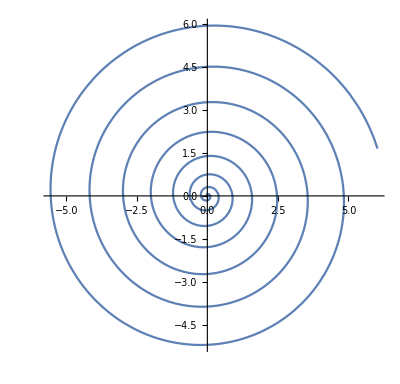

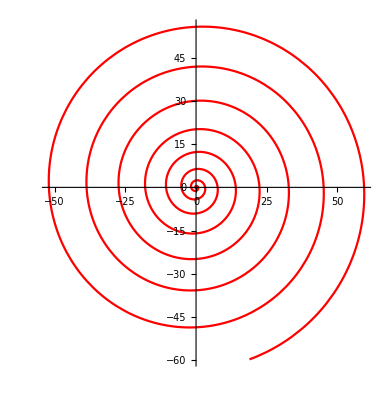

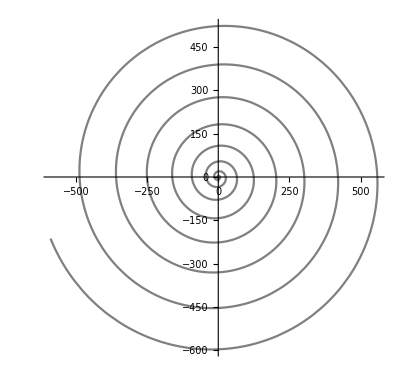

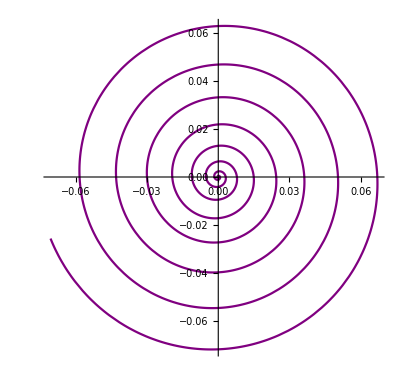

```mathematica
vals={a->.5,y0->0.01,Omega->10,mass->120*10^{-6}};
ParametricPlot[{r[[1]],r[[2]]}/.vals,{t,0,5}]
ParametricPlot[{vSA[[1]],vSA[[2]]}/.vals,{t,0,5},PlotStyle->Red]
ParametricPlot[{aSA[[1]],aSA[[2]]}/.vals,{t,0,5},PlotStyle->Gray]
ParametricPlot[{mass*aSA[[1]],mass*aSA[[2]]}/.vals,{t,0,5},PlotStyle->Purple]
```

## Problem 25.2

A turntable of radius L has an angular velocity of Omega in the +z direction in the lab frame. In the turntable frame, an ant starts at (-L,0,0) and walks in the positive x direction directly through the center of the turn table and to the opposite edge with a speed of v (also in the turntable frame). Determine the position, velocity, and acceleration of the ant as a function of time in the lab frame. Once again, we will do it first using the rotation matrix method, and second using the time derivative transformation formulas.

Let the radius of the turntable be L = 0.5 m and the velocity of the ant be v = 0.01 m/s.

```mathematica
Quit[]
```

```mathematica
Clear["`*"]
```

We call the lab S0 and the turntable S. To convert from turntable to lab coordinates, we need to use the rotation matrix R. < lab vector >= R < turntable vector > or < turntable vector >= R inverse < lab vector > .

```mathematica
R={{Cos[Omega*t],-Sin[Omega*t],0},{Sin[Omega*t],Cos[Omega*t],0},{0,0,1}};
R//MatrixForm
RI=FullSimplify[Inverse[R]];
RI//MatrixForm
FullSimplify[R.RI]//MatrixForm
```

(Cos[Omega t] | -Sin[Omega t] | 0
Sin[Omega t] | Cos[Omega t] | 0
0 | 0 | 1)

(Cos[Omega t] | Sin[Omega t] | 0
-Sin[Omega t] | Cos[Omega t] | 0
0 | 0 | 1)

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

First we find r0 in S0 by using the rotation matrix, and we differentiate it to find the velocity and acceleration.
Recall that the radius of the turntable is L.

```mathematica
r={-L+v t,0,0};r//MatrixForm
r0=R.r;r0//MatrixForm
vS0A=D[r0,t];vS0A//MatrixForm
aS0A=D[vS0A,t];aS0A//MatrixForm
```

(-L+t v
0
0)

((-L+t v) Cos[Omega t]
(-L+t v) Sin[Omega t]
0)

(v Cos[Omega t]-Omega (-L+t v) Sin[Omega t]
Omega (-L+t v) Cos[Omega t]+v Sin[Omega t]
0)

(-Omega^2 (-L+t v) Cos[Omega t]-2 Omega v Sin[Omega t]
2 Omega v Cos[Omega t]-Omega^2 (-L+t v) Sin[Omega t]
0)

### Solutions

```mathematica
r$={-L+v t,0,0};
r0$=R.r$;
vS0A$=FullSimplify[D[r0$,t]];
aS0A$=FullSimplify[D[vS0A$,t]];
If[FullSimplify[r]==FullSimplify[r$],Print["r is correct."],Print["r is incorrect."]]
If[FullSimplify[r0]==FullSimplify[r0$],Print["r0 is correct."],Print["r0 is incorrect."]]
If[FullSimplify[vS0A]==FullSimplify[vS0A$],Print["vS0A is correct."],Print["vS0A is incorrect."]]
If[FullSimplify[aS0A]==FullSimplify[aS0A$],Print["aS0A is correct."],Print["aS0A is incorrect."]]
```

r is correct.

r0 is correct.

vS0A is correct.

aS0A is correct.

Now we find v and a by the formulas. Note that the right hand sides are in terms of S unit vectors, so we need to rotate back to S0 to get the correct answers. vS01 is v in the S0 frame (found by the formula) but still in S components. vS02 is the result after rotation back to S0. Note that for the acceleration, I am giving you the answer, since we haven’t actually gone over the transformation of second derivatives in class yet. For your reference, I am using Equation 9.33.

Recall that Omega is the magnitude of the angular velocity.

```mathematica
vS={v,0,0};
aS={0,0,0};
Ovec={0,0,Omega};Ovec//MatrixForm
vS01=vS + Cross[Ovec,r];vS01//MatrixForm
vS02=Simplify[R.vS01];vS02//MatrixForm
aS01=aS+2 Cross[Ovec,vS]+Cross[Ovec,Cross[Ovec,r]];aS01//MatrixForm
aS02=FullSimplify[R.aS01];aS02//MatrixForm

(* check that the results agree *)
check1=FullSimplify[vS0A-vS02]
check2=FullSimplify[aS0A-aS02]
```

(0
0
Omega)

(v
-L Omega+Omega t v
0)

(v Cos[Omega t]+Omega (L-t v) Sin[Omega t]
-Omega (L-t v) Cos[Omega t]+v Sin[Omega t]
0)

(L Omega^2-Omega^2 t v
2 Omega v
0)

(Omega (Omega (L-t v) Cos[Omega t]-2 v Sin[Omega t])
Omega (2 v Cos[Omega t]+Omega (L-t v) Sin[Omega t])
0)

{0,0,0}

{0,0,0}

### Solutions

```mathematica
Ovec$={0,0,Omega};
vS$={v, 0,0};
aS$={0,0,0};
vS01$=vS$+Cross[Ovec$,r$];
vS02$=Simplify[R.vS01$];
aS01$=aS$+2 Cross[Ovec$,vS$]+Cross[Ovec$,Cross[Ovec$,r$]];
aS02$=FullSimplify[R.aS01$];

If[FullSimplify[Ovec$]==FullSimplify[Ovec],Print["Ovec is correct."],Print["Ovec is incorrect."]]
If[FullSimplify[vS$]==FullSimplify[vS],Print["vS0 is correct."],Print["vS0 is incorrect."]]
If[FullSimplify[aS$]==FullSimplify[aS],Print["aS0 is correct."],Print["aS0 is incorrect."]]
If[FullSimplify[vS01$]==FullSimplify[vS01],Print["vS1 is correct."],Print["vS1 is incorrect."]]
If[FullSimplify[vS02$]==FullSimplify[vS02],Print["vS2 is correct."],Print["vS2 is incorrect."]]
If[FullSimplify[aS01$]==FullSimplify[aS01],Print["aS1 is correct."],Print["aS1 is incorrect."]]
If[FullSimplify[aS02$]==FullSimplify[aS02],Print["aS2 is correct."],Print["aS2 is incorrect."]]
```

Ovec is correct.

vS0 is correct.

aS0 is correct.

vS1 is correct.

vS2 is correct.

aS1 is correct.

aS2 is correct.

Calculate the time tf required for the ant to complete its journey across the turntable. Derive a condition on Omega that will ensure that when the ant reaches the opposite side of the turntable, it will be at the same position in the lab frame it was when it started its journey. Plug in a value of Omega that satisfies this condition and verify that the ant ends up back where it started.

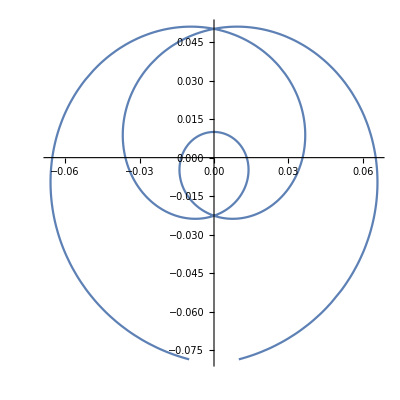

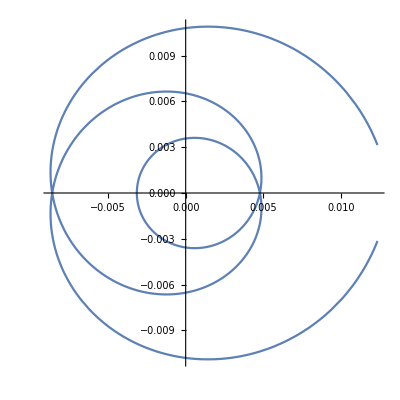

```mathematica
tf = 2*L/v;
vals={L->0.5,v->0.01,Omega->5*Pi*0.01/(2*0.5)};
Manipulate[ParametricPlot[{r0[[1]],r0[[2]]}/.vals,{t,0,tend},PlotRange->{{-0.55,0.55},{-0.55,0.55}},AspectRatio->1],{tend,0.01,tf/.vals}]
ParametricPlot[{vS0A[[1]],vS0A[[2]]}/.vals,{t,0,tf/.vals},AspectRatio->1]
ParametricPlot[{aS0A[[1]],aS0A[[2]]}/.vals,{t,0,tf/.vals},AspectRatio->1]
```

### Solutions

Time to cross the turntable: tf = 2 L/v
Condition on Omega: Omega = (odd integer)*Pi*v / (2 L)

## Written Problems

-Graphics-

```mathematica
DSolve[y''[t]==-g,y[t],t]
```

{{y[t]→-4.9 t^2+C[1]+t C[2]}}

```mathematica
DSolve[x''[t]==-A,x[t],t]
```

{{x[t]→-(A t^2)/2+C[1]+t C[2]}}